# Muon Beam Dump: BSM Scalar with FeynCalc

#### Notebook Description:

In this notebook, we go through calculations of cross sections for the production of beyond the Standard Model (BSM) states in a muon beam dump experiment, through scattering of the form
μ^-N → μ^- N ϕ_BSM
where ϕ_BSM indicates a BSM scalar.

We set up the relevant definitions and typesetting in Setup and perform calculations in Beam Dump Calculations.

Details:

In Beam Dump Calculations, we calculate cross sections both for the full/complicated 2→3 process as well as through the Weizsäcker-Williams approximation (which obtains an approximate result by sewing together a 1→2 process and a 2→2 process). Our calculations use FeynCalc, and rely on a model we design in the format of FeynRules and load using FeynArts.

# Setup

Setting up directories

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

### FeynCalc, Models, Typesetting

#### Loading FeynCalc and FeynArts

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

#### Initializing and Typesetting Model

Model Independent

```mathematica
MakeBoxes[epsel,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), e]\)";
MakeBoxes[epsmu,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(μ\)]\)";
```

Model Specific

```mathematica
InitializeModel["scalar_mubeamdump"];
```

loading generic model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/scalar_mubeamdump.mod

> 6 particles (incl. antiparticles) in 4 classes

> $CounterTerms are ON

> 4 vertices

classes model {scalar_mubeamdump} initialized

Names, couplings, etc.

```mathematica
MakeBoxes[phi,TraditionalForm]:="\!\(\(ϕ\)\)";

MakeBoxes[mBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(ϕ\)]\)";

MakeBoxes[gel,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[gmu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";
```

Kinematic Properties of the BSM final state:

```mathematica
MakeBoxes[EBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(ϕ\)]\)";
MakeBoxes[betaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(β\), \(ϕ\)]\)";
MakeBoxes[thetaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(θ\), \(ϕ\)]\)";
```

#### Other Typesetting

Outgoing lepton:

```mathematica
MakeBoxes[pprime,TraditionalForm]:="\!\(\*p'\)";
```

Beam and Target:

```mathematica
MakeBoxes[E0,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(0\)]\)";
MakeBoxes[mTar,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(T\)]\)";
```

SM Parameters:

```mathematica
MakeBoxes[mu,TraditionalForm]:="\!\(\*SubscriptBox[\(μ\)]\)";

MakeBoxes[mel,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), e]\)";
MakeBoxes[mmu,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(μ\)]\)";

MakeBoxes[alphaEM,TraditionalForm]:="\!\(\*SubscriptBox[\(α\), EM]\)";
```

#### Replacement Rules

```mathematica
BeamDumpCouplingRules = {gel->epsel e,gmu->epsmu e,e^2->4π alphaEM};
```

### 2→2 Kinematics

#### Typesetting

We denote the Mandelstam invariants for the effective 2 -> 2 process that emerges due to Weiszäcker-Williams (WW) with a subscript 2 :

```mathematica
MakeBoxes[s2,TraditionalForm]:="\!\(\*SubscriptBox[\(s\), \(2\)]\)";
MakeBoxes[t2,TraditionalForm]:="\!\(\*SubscriptBox[\(t\), \(2\)]\)";
MakeBoxes[u2,TraditionalForm]:="\!\(\*SubscriptBox[\(u\), \(2\)]\)";
```

They have counterparts with a tilde:

```mathematica
MakeBoxes[stilde,TraditionalForm]:="\!\(\*OverscriptBox[\(s\), \(~\)]\)";
MakeBoxes[ttilde,TraditionalForm]:="\!\(\*OverscriptBox[\(t\), \(~\)]\)";
MakeBoxes[utilde,TraditionalForm]:="\!\(\*OverscriptBox[\(u\), \(~\)]\)";
```

Furthermore, there are beam-related kinematic variables of interest:

#### Mandelstam and Kinematic Variable Setup

t (with no subscript) denotes the “momentum transfer” mediated by the intermediate WW photon:

```mathematica
t=-SP[q,q];
```

Mandelstam Setup with awesome built-in FeynCalc functions

```mathematica
SetMandelstam[s2, t2, u2,
p (* Incoming Lepton *),
q (* "Incoming" off-shell photon*),
-1*pprime (* Outgoing Lepton *),
-1*k (* Outgoing BSM Final State *),
 mmu (*Lepton*), q (*photon*), mmu (*Lepton*), mBSM (*BSM*)];
```

Replacements Involving 2 -> 2 Mandelstams :

```mathematica
TwoToTildeEl = {s2->stilde+mel^2,u2->utilde+mel^2};
TwoToTildeMu = {s2->stilde+mmu^2,u2->utilde+mmu^2};
```

```mathematica
TildeToTwoEl = {stilde->s2-mel^2,utilde->u2-mel^2};
TildeToTwoMu = {stilde->s2-mmu^2,utilde->u2-mmu^2};
```

#### “Limit Checker” Replacement Rules:

```mathematica
AllMassless = {mel->0,mmu->0,mBSM ->0,
(* also, zero virtuality for the WW photon: *)
SP[q,q]->0,SP[q,q]^2->0};
```

# Beam Dump Calculations

## 2→2 (Weizsäcker-Williams) Calculation

### (Squared) Amplitude

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

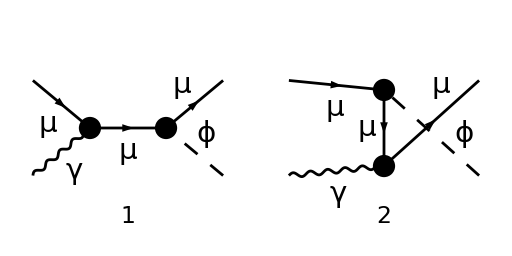

```mathematica
diagrams2to2= InsertFields[CreateTopologies[0, 2 -> 2], {F[2],V[1]} ->
		{F[2],S[1]}, InsertionLevel -> {Classes}, Model->"scalar_mubeamdump"];
Paint[diagrams2to2, ColumnsXRows -> {2, 1}, Numbering -> Simple,
	SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amplitude=FCFAConvert[CreateFeynAmp[diagrams2to2], IncomingMomenta->{p,q},
	OutgoingMomenta->{pprime,k},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q}, List->False, SMP->True,
	Contract->True];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

```mathematica
amplitudeSquared = (amplitude (ComplexConjugate[amplitude]))//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

```mathematica
amplitudeSquared
```

-((e^2 y_μ^2 (-m_ϕ^2 (2 m_μ^4 (q^2-5 (s_2+u_2))-2 m_μ^2 (q^2 (s_2+u_2)-2 s_2 u_2)+q^2 (s_2^2+u_2^2)+12 m_μ^6+2 s_2 u_2 (s_2+u_2))+(2 m_μ^2-s_2-u_2) (m_μ^4 (8 q^2-3 (s_2+u_2))+m_μ^2 (-4 q^2 (s_2+u_2)+s_2^2-4 s_2 u_2+u_2^2)+10 m_μ^6-s_2 u_2 (s_2+u_2))+2 m_ϕ^4 (m_μ^2-s_2) (m_μ^2-u_2)))/((m_μ^2-s_2)^2 (m_μ^2-u_2)^2))

### Applying Standard Formula for dσ/dt_2 in the Lab Frame

#### Setting up 2→2 Differential Cross Sections

Off-shell

```mathematica
var["dσ/dt_2"] = amplitudeSquared/(16π stilde^2)//.BeamDumpCouplingRules//.TwoToTildeMu//TrickMandelstam[#,{stilde,t2,utilde,q^2+mBSM^2}]&//FullSimplify;
var["dσ/(d (p . k))"] = 2var["dσ/dt_2"];
var["A^(2 → 2)"]=(stilde^2 var["dσ/(d (p . k))"])/(2π epsmu^2 alphaEM^2);
```

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell"] = var["dσ/(d (p . k))"]/.q^2->0;
var["A^(2 → 2) on-shell"]=(stilde^2 var["dσ/(d (p . k)) on-shell"])/(2π epsmu^2 alphaEM^2);
```

#### Explicit Expressions

Off-shell

```mathematica
var["dσ/dt_2"]
```

1/((s̃)^4 (ũ)^2)π α_EM^2 ϵ_μ^2 (m_ϕ^2 (q^2 ((s̃)^2+(ũ)^2)+2 m_μ^2 ((s̃)^2+6 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))-(s̃+ũ) (4 m_μ^2 (q^2 (s̃+ũ)+2 s̃ ũ)+8 m_μ^4 (s̃+ũ)+s̃ ũ (s̃+ũ))-2 s̃ ũ m_ϕ^4)

```mathematica
var["dσ/(d (p . k))"]
```

1/((s̃)^4 (ũ)^2)2 π α_EM^2 ϵ_μ^2 (m_ϕ^2 (q^2 ((s̃)^2+(ũ)^2)+2 m_μ^2 ((s̃)^2+6 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))-(s̃+ũ) (4 m_μ^2 (q^2 (s̃+ũ)+2 s̃ ũ)+8 m_μ^4 (s̃+ũ)+s̃ ũ (s̃+ũ))-2 s̃ ũ m_ϕ^4)

```mathematica
var["A^(2 → 2)"]
```

1/((s̃)^2 (ũ)^2)(m_ϕ^2 (q^2 ((s̃)^2+(ũ)^2)+2 m_μ^2 ((s̃)^2+6 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))-(s̃+ũ) (4 m_μ^2 (q^2 (s̃+ũ)+2 s̃ ũ)+8 m_μ^4 (s̃+ũ)+s̃ ũ (s̃+ũ))-2 s̃ ũ m_ϕ^4)

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell"]
```

1/((s̃)^4 (ũ)^2)2 π α_EM^2 ϵ_μ^2 (m_ϕ^2 (2 m_μ^2 ((s̃)^2+6 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))-(s̃+ũ) (8 m_μ^4 (s̃+ũ)+8 s̃ ũ m_μ^2+s̃ ũ (s̃+ũ))-2 s̃ ũ m_ϕ^4)

```mathematica
var["A^(2 → 2) on-shell"]
```

1/((s̃)^2 (ũ)^2)(m_ϕ^2 (2 m_μ^2 ((s̃)^2+6 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))-(s̃+ũ) (8 m_μ^4 (s̃+ũ)+8 s̃ ũ m_μ^2+s̃ ũ (s̃+ũ))-2 s̃ ũ m_ϕ^4)

### Applying Kinematic Approximations

#### Stating Approximations:

```mathematica
tMinApproximations = {
stilde->-utilde/(1-x),
utilde->-x E0^2 thetaBSM^2-mBSM^2(1-x)/x-mmu^2 x,
t2->(utilde x)/(1-x)+mBSM^2,
SP[q,q]->-stilde^2/(4 E0^2)
};
```

#### Applying Approximations

Off-shell

```mathematica
var["dσ/(d (p . k)) near tmin"] =var["dσ/(d (p . k))"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) near tmin"]=(stilde^2 var["dσ/(d (p . k)) near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"] =var["dσ/(d (p . k)) on-shell"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) on-shell near tmin"]=(stilde^2 var["dσ/(d (p . k)) on-shell near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

#### Explicit Expressions

Off-Shell

```mathematica
var["dσ/(d (p . k)) near tmin"]
```

(π α_EM^2 ϵ_μ^2 x^2 (2 m_ϕ^4 (x-1) x^2 (E_0^2 (θ_ϕ^2 ((x-2) x+2)-2 (x-1)^2)+m_μ^2 x^2)-m_ϕ^2 x^4 (E_0^4 θ_ϕ^4 ((x-2) x+2)+2 E_0^2 m_μ^2 (θ_ϕ^2 (x (x+2)-2)-4 (x-1)^2)+m_μ^4 (x (x+6)-6))+4 x^4 (E_0^6 (-θ_ϕ^4) (x-1) x^2+E_0^4 θ_ϕ^2 m_μ^2 (x (x (θ_ϕ^2-2 x+10)-16)+8)+E_0^2 m_μ^4 x^2 (2 θ_ϕ^2-x+1)+m_μ^6 x^2)+m_ϕ^6 (-(x-1)^2) ((x-2) x+2)))/(2 E_0^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4)

```mathematica
var["A^(2 → 2) near tmin"]//FullSimplify
```

-((-2 m_ϕ^4 (x-1) x^2 (E_0^2 (θ_ϕ^2 ((x-2) x+2)-2 (x-1)^2)+m_μ^2 x^2)+m_ϕ^2 x^4 (E_0^4 θ_ϕ^4 ((x-2) x+2)+2 E_0^2 m_μ^2 (θ_ϕ^2 (x (x+2)-2)-4 (x-1)^2)+m_μ^4 (x (x+6)-6))+4 x^4 (E_0^6 θ_ϕ^4 (x-1) x^2-E_0^4 θ_ϕ^2 m_μ^2 (x (x (θ_ϕ^2-2 x+10)-16)+8)+E_0^2 m_μ^4 x^2 (-2 θ_ϕ^2+x-1)-m_μ^6 x^2)+m_ϕ^6 (x-1)^2 ((x-2) x+2))/(4 E_0^2 (x-1)^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2))

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"]
```

-((2 π α_EM^2 ϵ_μ^2 (x-1) x^4 (x^2 (E_0^4 θ_ϕ^4 x^2+2 E_0^2 θ_ϕ^2 m_μ^2 (x-2)^2+m_μ^4 x^2)-2 m_μ^2 m_ϕ^2 (x-1) x^2+m_ϕ^4 (x-1)^2))/(m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4)

```mathematica
var["A^(2 → 2) on-shell near tmin"]//FullSimplify
```

-((x^2 (x^2 (E_0^4 θ_ϕ^4 x^2+2 E_0^2 θ_ϕ^2 m_μ^2 (x-2)^2+m_μ^4 x^2)-2 m_μ^2 m_ϕ^2 (x-1) x^2+m_ϕ^4 (x-1)^2))/((x-1) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2))

# Saving Results

Putting everything into a single function

```mathematica
var["Squared, Spin-Averaged Matrix Element"]=amplitudeSquared;
var["Squared, Spin-Averaged Matrix Element on-shell"]=amplitudeSquared//.SP[q,q]->0;
```

```mathematica
keys = {"Squared, Spin-Averaged Matrix Element",
"Squared, Spin-Averaged Matrix Element on-shell",
"dσ/(d (p . k))", "dσ/(d (p . k)) on-shell",
"dσ/(d (p . k)) near tmin", "dσ/(d (p . k)) on-shell near tmin",
"A^(2 → 2)", "A^(2 → 2) on-shell",
"A^(2 → 2) near tmin", "A^(2 → 2) on-shell near tmin"};
```

```mathematica
Do[scalar2to2[keys[[i]]]=var[keys[[i]]],{i,Length[keys]}]

(* For debugging: *)
(*scalar2to2/@keys*)
```

Saving all functions

```mathematica
Put[FullDefinition[scalar2to2],$scalar2to2Functions]
```

```mathematica
PutAppend[FullDefinition[tMinApproximations], $scalar2to2Functions]
```

```mathematica
Quit[]
```